## Active polymer driven by inhomogeneous excitations

This notebook illustrates the effects of sinusoidal activity modulations (that is, we deal with a diagonal correlation function) on the polymer conformation, and shows how these excitations elicit effective long-ranged interactions.

Load required packages.

```mathematica
Once@AppendTo[$Path,NotebookDirectory[]<>"Source/Diagonal/"];
Needs["KernelActivity`"->None,"KernelActivity.wl"]
Needs["KernelTension`"->None,"KernelTension.wl"]
Needs["KernelGeneric`"->None,"KernelGeneric.wl"]
Needs["AnalyticCosine`"->None,"AnalyticCosine.wl"]
```

Set parameters and determine functions that we will later plot: “response”, which is the mean squared separation in response to an activity profile; “baseline”, which assumes a constant activity; “shape”, which is the tangent autocorrelation function; “interaction”, which shows the effective harmonic interactions.

```mathematica
a=1; (* Length scale of sinusoidal activity modulations*)
EPS=0.5; (* Magnitude of sinusoidal activity modulations*)
TEN=0; (* Magnitude of sinusoidal tension modulations*)

response[x_,y_]=AnalyticCosine`SquaredSeparation[x,y,κ->0,"ActivityMagnitude"->EPS,"TensionMagnitude"->TEN];
baseline[x_,y_]=AnalyticCosine`SquaredSeparation[x,y,κ->0];
shape[x_,y_]=AnalyticCosine`TangentCorrelation[x,y,κ->0,"ActivityMagnitude"->EPS,"TensionMagnitude"->TEN];
interaction[x_,y_]=Module[{fun},
fun[x_]=KernelGeneric`StiffnessActivity[x,a];
Cos[a(x+y)/2]*fun[Abs[x-y]]];

upperleft[x_,y_]:=Re[response[x,y]/baseline[x,y]-1];
lowerright[x_,y_]:=Re[response[x,y]];
```

Plot the relative mean squared separation between different points.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

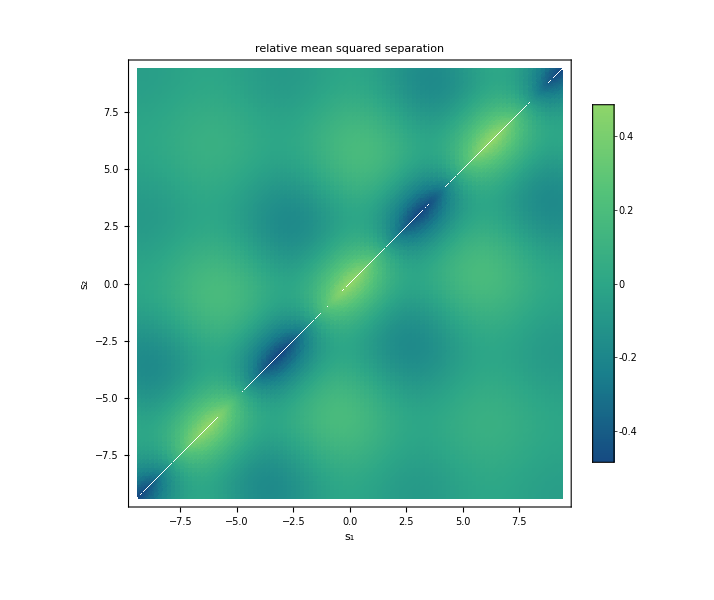

```mathematica
relrange=0.75;
colorlist=ColorData["BlueGreenYellow"]/@Table[x,{x,0,1,1/255}];

DensityPlot[
upperleft[x,y],
{x,-3Pi,3Pi},{y,-3Pi,3Pi},
ColorFunctionScaling->False,
ColorFunction->(Blend[colorlist,Rescale[#,{-relrange,relrange}]]&),
ImageSize->600,
Background->None,
PlotRange->{{-3Pi,3Pi},{-3Pi,3Pi},{-relrange,relrange}},
PlotPoints->100,
PlotLegends->Automatic,
PlotLabel->"relative mean squared separation",
FrameLabel->{Subscript[s, 1],Subscript[s, 2]}
]
```

Plot the absolute mean squared separation between different points.

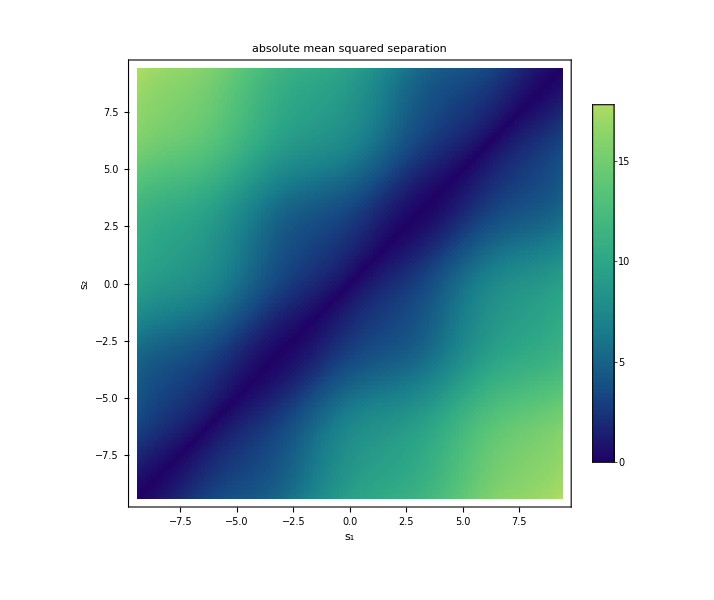

```mathematica
absrange=20;
colorlist=ColorData["BlueGreenYellow"]/@Table[x,{x,0,1,1/255}];

DensityPlot[
lowerright[x,y],
{x,-3Pi,3Pi},{y,-3Pi,3Pi},
ColorFunctionScaling->False,
ColorFunction->(Blend[colorlist,Rescale[#,{0,absrange}]]&),
ImageSize->600,
Background->None,
PlotRange->{{-3Pi,3Pi},{-3Pi,3Pi},{0,absrange}},
PlotPoints->100,
PlotLegends->Automatic,
PlotLabel->"absolute mean squared separation",
FrameLabel->{Subscript[s, 1],Subscript[s, 2]}
]
```

Plot the tangent correlation between different points.

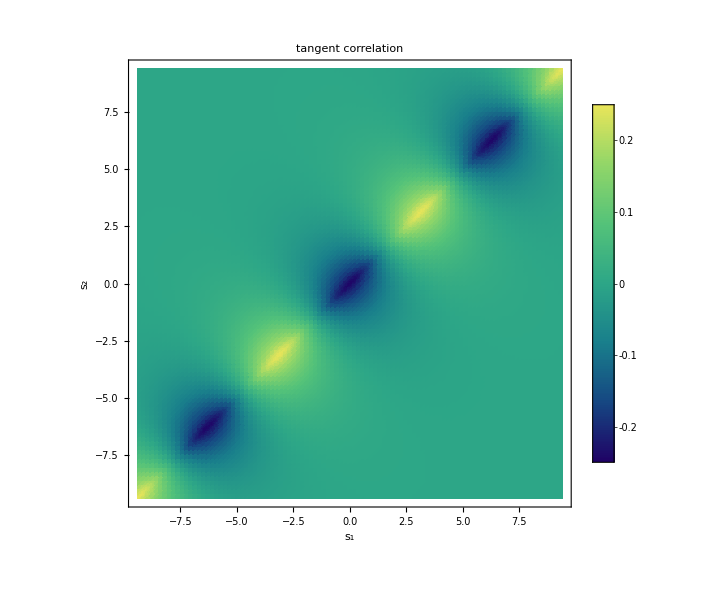

```mathematica
ttrange=0.25;
colorlist=ColorData["BlueGreenYellow"]/@Table[x,{x,0,1,1/255}];

DensityPlot[
shape[x,y],
{x,-3Pi,3Pi},{y,-3Pi,3Pi},
ColorFunctionScaling->False,
ColorFunction->(Blend[colorlist,Rescale[#,{-ttrange,ttrange}]]&),
ImageSize->600,
Background->None,
PlotRange->{{-3Pi,3Pi},{-3Pi,3Pi},{-ttrange,ttrange}},
PlotPoints->100,
PlotLegends->Automatic,
PlotLabel->"tangent correlation",
FrameLabel->{Subscript[s, 1],Subscript[s, 2]}
]
```

Plot the effective interactions between different points.

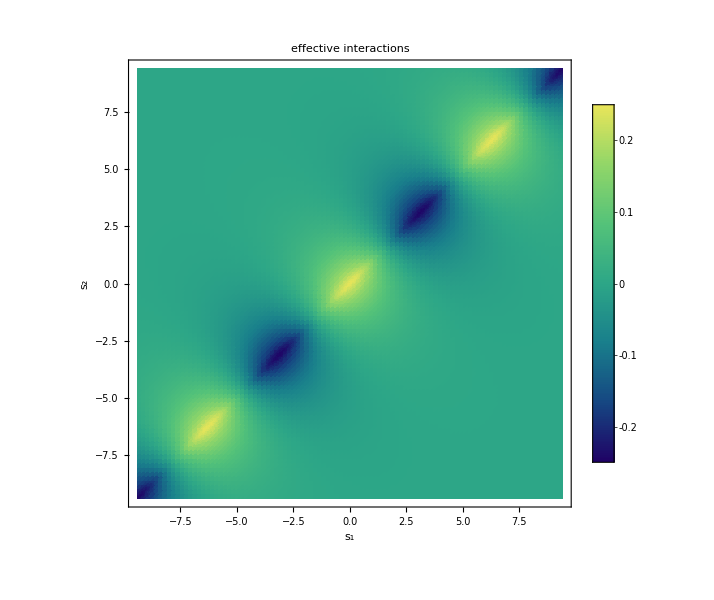

```mathematica
interactionrange=0.25;
colorlist=ColorData["BlueGreenYellow"]/@Table[x,{x,0,1,1/255}];

DensityPlot[
interaction[x,y],
{x,-3Pi,3Pi},{y,-3Pi,3Pi},
ColorFunctionScaling->False,
ColorFunction->(Blend[colorlist,Rescale[#,{-interactionrange,interactionrange}]]&),
ImageSize->600,
Background->None,
PlotRange->{{-3Pi,3Pi},{-3Pi,3Pi},{-interactionrange,interactionrange}},
PlotPoints->100,
PlotLegends->Automatic,
PlotLabel->"effective interactions",
FrameLabel->{Subscript[s, 1],Subscript[s, 2]}
]
```